```mathematica
(*Quadratic demand: D(p) = max(1 - p/c, 0)^2*)
```

```mathematica
Clear["Global`*"]
```

```mathematica
(*Two customers: c1 < c2 < 3c1, a1 = a2 = 1*)
```

```mathematica
(*Define the revenue and surplus*)
Rev[p_, c_]:=p*(1 - p/c)^2;
Sur[p_, c_]:=(c-p)^3/(3c^2);
```

```mathematica
(*The optimal prices of customer 1 and 2*)
sol1 = Solve[D[Rev[p,c1],p]==0,{p}];
p1 = p/.sol1[[1]]

sol2 = Solve[D[Rev[p,c2],p]==0,{p}];
p2 = p/.sol2[[1]]
```

c1/3

c2/3

```mathematica
(*Revenue change due to new common price p*)
R =(Rev[p, c1]+ Rev[p, c2])-(Rev[p1, c1] + Rev[p2, c2])
```

-(4 c1)/27-(4 c2)/27+p (1-p/c1)^2+p (1-p/c2)^2

```mathematica
(*Surplus change due to new common price p*)
```

```mathematica
S =(Sur[p, c1]+ Sur[p, c2])-(Sur[p1, c1] + Sur[p2, c2])
```

-(8 c1)/81-(8 c2)/81+(c1-p)^3/(3 c1^2)+(c2-p)^3/(3 c2^2)

```mathematica
(*Find the optimal new common price*)
```

```mathematica
Solve[D[R,p]==0,{p}]
```

{{p→(2/c1+2/c2-(√2 √(-c1^2+4 c1 c2-c2^2))/(c1 c2))/(3 (1/c1^2+1/c2^2))},{p→(2/c1+2/c2+(√2 √(-c1^2+4 c1 c2-c2^2))/(c1 c2))/(3 (1/c1^2+1/c2^2))}}

```mathematica
p=(2/c1+2/c2-(√2 √(-c1^2+4 c1 c2-c2^2))/(c1 c2))/(3 (1/c1^2+1/c2^2))
```

(2/c1+2/c2-(√2 √(-c1^2+4 c1 c2-c2^2))/(c1 c2))/(3 (1/c1^2+1/c2^2))

```mathematica
(*The social welfare change due to new common price p*)
Simplify[R]
W = Simplify[R + S]
```

-(4 (c1^5-4 c1^4 c2+c2^5+c1^2 c2^2 (5 c2-4 √2 √(-c1^2+4 c1 c2-c2^2))+c1 c2^3 (-4 c2+√2 √(-c1^2+4 c1 c2-c2^2))+c1^3 c2 (5 c2+√2 √(-c1^2+4 c1 c2-c2^2))))/(27 (c1^2+c2^2)^2)

(7 c1^5-19 c1^4 c2+7 c2^5+4 c1^2 c2^2 (-7 c2+2 √2 √(-c1^2+4 c1 c2-c2^2))+4 c1^3 c2 (-7 c2+4 √2 √(-c1^2+4 c1 c2-c2^2))+c1 c2^3 (-19 c2+16 √2 √(-c1^2+4 c1 c2-c2^2)))/(81 (c1^2+c2^2)^2)

```mathematica
Simplify[Coefficient[W, √2 √(-c1^2+4 c1 c2-c2^2)]]
```

(8 c1 c2 (2 c1^2+c1 c2+2 c2^2))/(81 (c1^2+c2^2)^2)

```mathematica
Simplify[W - (8 c1 c2 (2 c1^2+c1 c2+2 c2^2))/(81 (c1^2+c2^2)^2)*√2 √(-c1^2+4 c1 c2-c2^2)]
```

-(-7 c1^5+19 c1^4 c2+28 c1^3 c2^2+28 c1^2 c2^3+19 c1 c2^4-7 c2^5)/(81 (c1^2+c2^2)^2)

```mathematica
(*To determine when W > 0, split w into two parts, W1 > 0, and W2 < 0*)
W1 = (8 c1 c2 (2 c1^2+c1 c2+2 c2^2))/(81 (c1^2+c2^2)^2)*√2 √(-c1^2+4 c1 c2-c2^2);
W2 = -(-7 c1^5+19 c1^4 c2+28 c1^3 c2^2+28 c1^2 c2^3+19 c1 c2^4-7 c2^5)/(81 (c1^2+c2^2)^2);
```

```mathematica
Simplify[W1^2 - W2^2]
```

-((c1-c2)^2 (49 c1^4-168 c1^3 c2-2 c1^2 c2^2-168 c1 c2^3+49 c2^4))/(6561 (c1^2+c2^2)^2)

```mathematica
(*To determine whether W1 > W2, let c2 = k*c1 *)
c2 = k*c1;
Simplify[W1^2 - W2^2]
```

-(c1^2 (-1+k)^2 (49-168 k-2 k^2-168 k^3+49 k^4))/(6561 (1+k^2)^2)

```mathematica
(*From the following graph we can see that when c2 < 3c1, the social welfare change is always positive*)
```

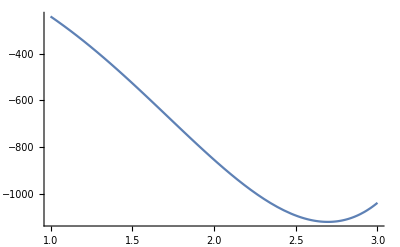

```mathematica
Plot[49-168 k-2 k^2-168 k^3+49 k^4, {k, 1, 3}]
```

```mathematica
Clear["Global`*"]
```

```mathematica
(*Two customers: 3c1 < c2, a1 = a2 = 1*)
(*The optimal price may be >= c1, i.e., the optimal price may be p2*)
(*Compare which one's revenue change is less*)
```

```mathematica
(*Define the revenue and surplus*)
Rev[p_, c_]:=p*(1 - p/c)^2;
Sur[p_, c_]:=(c-p)^3/(3c^2);
```

```mathematica
(*The optimal prices of customer 1 and 2*)
p1 = c1/3;
p2 = c2/3;
```

```mathematica
(*Revenue change due to the fairness constraint*)
```

```mathematica
R = -Rev[p1, c1]
```

-(4 c1)/27

```mathematica
(*Surplus change due to the fairness constraint*)
```

```mathematica
S = - Sur[p1, c1]
```

-(8 c1)/81

```mathematica
(*Social welfare change due the fairness constraint*)
```

```mathematica
W = Simplify[R + S]
```

-(20 c1)/81

```mathematica
Clear["Global`*"]
```

```mathematica
(*If the optimal new price is p2, the change of social welfare is always negative*)
```

```mathematica
(*Solve for the condition that the optimal new price lies in [0, c1]*)
```

```mathematica
R1 = -(4 (c1^5-4 c1^4 c2+c2^5+c1^2 c2^2 (5 c2-4 √2 √(-c1^2+4 c1 c2-c2^2))+c1 c2^3 (-4 c2+√2 √(-c1^2+4 c1 c2-c2^2))+c1^3 c2 (5 c2+√2 √(-c1^2+4 c1 c2-c2^2))))/(27 (c1^2+c2^2)^2)
R2 = -(4 c1)/27
```

-(4 (c1^5-4 c1^4 c2+c2^5+c1^2 c2^2 (5 c2-4 √2 √(-c1^2+4 c1 c2-c2^2))+c1 c2^3 (-4 c2+√2 √(-c1^2+4 c1 c2-c2^2))+c1^3 c2 (5 c2+√2 √(-c1^2+4 c1 c2-c2^2))))/(27 (c1^2+c2^2)^2)

-(4 c1)/27

```mathematica
(*The optimal new price lies in [0, c1] if R1 <= R2*)
```

```mathematica
Simplify[R1 - R2]
```

-(4 c2 (-4 c1^4+c2^4+c1^2 c2 (5 c2-4 √2 √(-c1^2+4 c1 c2-c2^2))+c1 c2^2 (-5 c2+√2 √(-c1^2+4 c1 c2-c2^2))+c1^3 (3 c2+√2 √(-c1^2+4 c1 c2-c2^2))))/(27 (c1^2+c2^2)^2)

```mathematica
Simplify[Coefficient[R1-R2, √2 √(-c1^2+4 c1 c2-c2^2)]]
```

-(4 c1 c2 (c1^2-4 c1 c2+c2^2))/(27 (c1^2+c2^2)^2)

```mathematica
Simplify[R1 - R2 - (-(4 c1 c2 (c1^2-4 c1 c2+c2^2))/(27 (c1^2+c2^2)^2)*√2 √(-c1^2+4 c1 c2-c2^2))]
```

-(4 c2 (-4 c1^4+3 c1^3 c2+5 c1^2 c2^2-5 c1 c2^3+c2^4))/(27 (c1^2+c2^2)^2)

```mathematica
DR1 = -(4 c1 c2 (c1^2-4 c1 c2+c2^2))/(27 (c1^2+c2^2)^2)*√2 √(-c1^2+4 c1 c2-c2^2)
DR2 = -(4 c2 (-4 c1^4+3 c1^3 c2+5 c1^2 c2^2-5 c1 c2^3+c2^4))/(27 (c1^2+c2^2)^2)
```

-(4 √2 c1 c2 √(-c1^2+4 c1 c2-c2^2) (c1^2-4 c1 c2+c2^2))/(27 (c1^2+c2^2)^2)

-(4 c2 (-4 c1^4+3 c1^3 c2+5 c1^2 c2^2-5 c1 c2^3+c2^4))/(27 (c1^2+c2^2)^2)

```mathematica
Simplify[DR1^2 - DR2^2]
```

-(16 c2^2 (-3 c1+c2)^2 (2 c1^2-4 c1 c2+c2^2))/(729 (c1^2+c2^2)^2)

```mathematica
(*Conclusion: R1 >= R2 if and only if 2 c1^2 - 4c1*c2 + c2^2 < 0, i.e., c2 <= (2 + √3)*)
```

```mathematica
Clear["Global`*"]
```

```mathematica
(*Two customers: c1 < c2 < 3c1, a2/a1 = a*)
```

```mathematica
(*Define the revenue and surplus*)
Rev[p_, c_]:=p*(1 - p/c)^2;
Sur[p_, c_]:=(c-p)^3/(3c^2);
```

```mathematica
(*The optimal prices of customer 1 and 2*)
sol1 = Solve[D[Rev[p,c1],p]==0,{p}];
p1 = p/.sol1[[1]]

sol2 = Solve[D[Rev[p,c2],p]==0,{p}];
p2 = p/.sol2[[1]]
```

c1/3

c2/3

```mathematica
(*Revenue change due to new common price p*)
R =(Rev[p, c1]+ a*Rev[p, c2])-(Rev[p1, c1] + a*Rev[p2, c2])
```

-(4 c1)/27-(4 a c2)/27+p (1-p/c1)^2+a p (1-p/c2)^2

```mathematica
(*Surplus change due to new common price p*)
```

```mathematica
S =(Sur[p, c1]+ a*Sur[p, c2])-(Sur[p1, c1] + a*Sur[p2, c2])
```

-(8 c1)/81-(8 a c2)/81+(c1-p)^3/(3 c1^2)+(a (c2-p)^3)/(3 c2^2)

```mathematica
(*Find the optimal new common price*)
```

```mathematica
Solve[D[R,p]==0,{p}]
```

{{p→(2/c1+(2 a)/c2-(√(-3 a c1^2+a^2 c1^2+8 a c1 c2+c2^2-3 a c2^2))/(c1 c2))/(3 (1/c1^2+a/c2^2))},{p→(2/c1+(2 a)/c2+(√(-3 a c1^2+a^2 c1^2+8 a c1 c2+c2^2-3 a c2^2))/(c1 c2))/(3 (1/c1^2+a/c2^2))}}

```mathematica
p=(2/c1+(2 a)/c2-(√(-3 a c1^2+a^2 c1^2+8 a c1 c2+c2^2-3 a c2^2))/(c1 c2))/(3 (1/c1^2+a/c2^2))
```

(2/c1+(2 a)/c2-(√(-3 a c1^2+a^2 c1^2+8 a c1 c2+c2^2-3 a c2^2))/(c1 c2))/(3 (1/c1^2+a/c2^2))

```mathematica
(*The social welfare change due to new common price p*)
Simplify[R]
W = Simplify[R + S]
```

-1/(27 (a c1^2+c2^2)^2)2 (a^3 c1^4 c2+c1 c2^3 (c2-√(-3 a c1^2+a^2 c1^2+8 a c1 c2+c2^2-3 a c2^2))+a^2 c1^2 (2 c1^3-9 c1^2 c2-5 c2^3+c1 c2 (15 c2-√(-3 a c1^2+a^2 c1^2+8 a c1 c2+c2^2-3 a c2^2)))+a c2 (2 c2^4+c1^2 c2 (15 c2-8 √(-3 a c1^2+a^2 c1^2+8 a c1 c2+c2^2-3 a c2^2))+3 c1 c2^2 (-3 c2+√(-3 a c1^2+a^2 c1^2+8 a c1 c2+c2^2-3 a c2^2))+c1^3 (-5 c2+3 √(-3 a c1^2+a^2 c1^2+8 a c1 c2+c2^2-3 a c2^2))))

1/(81 (a c1^2+c2^2)^2)(-10 a^3 c1^4 c2+10 c1 c2^3 (-c2+√(-3 a c1^2+a^2 c1^2+8 a c1 c2+c2^2-3 a c2^2))+a c2 (7 c2^4+3 c1 c2^2 (-3 c2+2 √(-3 a c1^2+a^2 c1^2+8 a c1 c2+c2^2-3 a c2^2))+c1^3 (5 c2+6 √(-3 a c1^2+a^2 c1^2+8 a c1 c2+c2^2-3 a c2^2))+c1^2 c2 (-33 c2+8 √(-3 a c1^2+a^2 c1^2+8 a c1 c2+c2^2-3 a c2^2)))+a^2 c1^2 (7 c1^3-9 c1^2 c2+5 c2^3+c1 c2 (-33 c2+10 √(-3 a c1^2+a^2 c1^2+8 a c1 c2+c2^2-3 a c2^2))))

```mathematica
Simplify[Coefficient[W, √(-3 a c1^2+a^2 c1^2+8 a c1 c2+c2^2-3 a c2^2)]]
```

(2 c1 c2 (5 a^2 c1^2+5 c2^2+a (3 c1^2+4 c1 c2+3 c2^2)))/(81 (a c1^2+c2^2)^2)

```mathematica
Simplify[W - (2 c1 c2 (5 a^2 c1^2+5 c2^2+a (3 c1^2+4 c1 c2+3 c2^2)))/(81 (a c1^2+c2^2)^2)*√(-3 a c1^2+a^2 c1^2+8 a c1 c2+c2^2-3 a c2^2)]
```

(-10 a^3 c1^4 c2-10 c1 c2^4+a^2 c1^2 (7 c1^3-9 c1^2 c2-33 c1 c2^2+5 c2^3)+a c2^2 (5 c1^3-33 c1^2 c2-9 c1 c2^2+7 c2^3))/(81 (a c1^2+c2^2)^2)

```mathematica
(*To determine when W > 0, split w into two parts, W1 > 0, and W2 < 0*)
W1 = (2 c1 c2 (5 a^2 c1^2+5 c2^2+a (3 c1^2+4 c1 c2+3 c2^2)))/(81 (a c1^2+c2^2)^2)*√(-3 a c1^2+a^2 c1^2+8 a c1 c2+c2^2-3 a c2^2);
W2 =(-10 a^3 c1^4 c2-10 c1 c2^4+a^2 c1^2 (7 c1^3-9 c1^2 c2-33 c1 c2^2+5 c2^3)+a c2^2 (5 c1^3-33 c1^2 c2-9 c1 c2^2+7 c2^3))/(81 (a c1^2+c2^2)^2);
```

```mathematica
Simplify[W1^2 - W2^2]
```

(a (c1-c2)^2 (20 a^2 c1^2 (7 c1-4 c2) c2+20 c1 c2^2 (-4 c1+7 c2)+a (-49 c1^4+28 c1^3 c2+162 c1^2 c2^2+28 c1 c2^3-49 c2^4)))/(6561 (a c1^2+c2^2)^2)

```mathematica
c2 = k*c1;
Simplify[W1^2 - W2^2]
```

-(a c1^2 (-1+k)^2 (20 (4-7 k) k^2+20 a^2 k (-7+4 k)+a (49-28 k-162 k^2-28 k^3+49 k^4)))/(6561 (a+k^2)^2)

```mathematica
(*Note if 1 < k < 7/4, then 20 (4-7 k) k^2 < 0, 20 a^2 k (-7+4 k) < 0, and a (49-28 k-162 k^2-28 k^3+49 k^4) < 0*)
(*Therefore, when k < 7/4, W > 0*)
```